# economic analysis

## import data

(1) raw data frequency

(2) status quo full
(3) stewardship full
(4) status quo w/ uncertainty bands
(5) stewardship w/ uncertainty bands

(6) status quo- best fit
(7) stewardship- best fit

(8) steady state full
(9) steady state w/ uncertainty bands
(10) steady state- best fit

(11) SQ- switch year
(12) stewardship- switch year

(13) mortality (R, S, A)

### preparing directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCeaalls"]]}];
```

### load data

```mathematica
nod=3; (*# of diagnoses*)

(*MODEL OUTPUTS*)
Quiet[dataP=ToExpression[Import["pneumonia output.xlsx","Data"]]; (*pneumonia*)
dataS=ToExpression[Import["sepsis output.xlsx","Data"]]; (*sepsis*)
dataU=ToExpression[Import["uti output.xlsx","Data"]];] (*uti*)
```

*note to ask Meagan- how do I plot the uncertainty band? Currently- just taking min and max of each point

**need to take 95% of the 100 sampled?

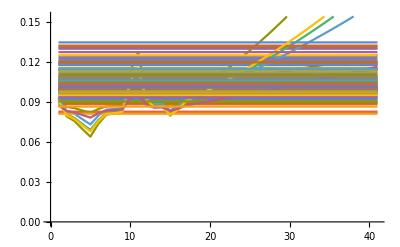

```mathematica
ListLinePlot[
dataU[[2]][[2]]]
```

```mathematica
(*DATA & PARAMETERS*)
mdataP=Import["AMR_Datasheet.xlsx",{"Data","Pneu_model"}]; (*PNEUMONIA*)
mdataP = mdataP[[All,2;;]]; 
years = mdataP[[1]]; (*years of available data*)
tt = Length[years];  (*# years of available data*)
pathogens=mdataP[[15]][[1;;3]]; (*pathogen headers*)
nop = Length[pathogens]; (*# of pathogens*)
cbpP=mdataP[[-5]][[-1]]; (*proportion of pneumonia patients prescribed cbps*)
inappP=mdataP[[-4]][[1]]; (*inappropriate cbp prescription*)
pathP=Table[mdataP[[i]][[-1]],{i,18,20}]; 
(*proportion of pneumonia for PA, AB, KP*)

edataP=mdataP[[21;;]];(*data for economic and health outcomes*) 
stw = edataP[[1]][[1]]; (*reduction in inappropriate therapy*)
pP=edataP[[13]];  (*prevalence of pneumonia*)

mdataS=Import["AMR_Datasheet.xlsx",{"Data","Sepsis_model"}]; (*SEPSIS*)
mdataS = mdataS[[All,2;;]]; 
cbpS=mdataS[[11]][[-1]]; (*proportion of pneumonia patients prescribed cbps*)
inappS=mdataS[[12]][[1]]; (*inappropriate cbp prescription*)
pathS=Table[mdataS[[i]][[-1]],{i,13,15}]; 
(*proportion of pneumonia for PA, AB, KP*)

edataS=mdataS[[21;;]];(*data for economic and health outcomes*)
pS=edataS[[13]]; (*prevalence of sepsis*)

mdataU=Import["AMR_Datasheet.xlsx",{"Data","UTI_model"}]; (*UTI*)
mdataU = mdataU[[All,2;;]]; 
cbpU=mdataU[[11]][[-1]]; (*proportion of pneumonia patients prescribed cbps*)
inappU=mdataU[[12]][[1]]; (*inappropriate cbp prescription*)
pathU=Table[mdataU[[i]][[-1]],{i,13,15}]; 
(*proportion of pneumonia for PA, AB, KP*)

edataU=mdataU[[21;;]];(*data for economic and health outcomes*)
pU=edataU[[13]]; (*prevalence of UTI*)

p={pP,pS,pU}; (*prevalence*)
```

## model fit plots & projections

### plot raw data + uncertainty

```mathematica
meanP={Mean[dataP[[1]][[1]]],Mean[dataP[[1]][[2]]],Mean[dataP[[1]][[3]]]}; 
sdP={Table[StandardDeviation[Flatten[Table[Transpose[dataP[[1]][[1]][[i]]][[2]][[t]],{i,1,1000}]]],{t,1,tt}],
Table[StandardDeviation[Flatten[Table[Transpose[dataP[[1]][[2]][[i]]][[2]][[t]],{i,1,1000}]]],{t,1,tt}],
Table[StandardDeviation[Flatten[Table[Transpose[dataP[[1]][[3]][[i]]][[2]][[t]],{i,1,1000}]]],{t,1,tt}]};

meanS={Mean[dataS[[1]][[1]]],Mean[dataS[[1]][[2]]],Mean[dataS[[1]][[3]]]}; 
sdS={Table[StandardDeviation[Flatten[Table[Transpose[dataS[[1]][[1]][[i]]][[2]][[t]],{i,1,1000}]]],{t,1,tt}],
Table[StandardDeviation[Flatten[Table[Transpose[dataS[[1]][[2]][[i]]][[2]][[t]],{i,1,1000}]]],{t,1,tt}],
Table[StandardDeviation[Flatten[Table[Transpose[dataS[[1]][[3]][[i]]][[2]][[t]],{i,1,1000}]]],{t,1,tt}]};

meanU={Mean[dataU[[1]][[1]]],Mean[dataU[[1]][[2]]],Mean[dataU[[1]][[3]]]}; 
sdU={Table[StandardDeviation[Flatten[Table[Transpose[dataU[[1]][[1]][[i]]][[2]][[t]],{i,1,1000}]]],{t,1,tt}],
Table[StandardDeviation[Flatten[Table[Transpose[dataU[[1]][[2]][[i]]][[2]][[t]],{i,1,1000}]]],{t,1,tt}],
Table[StandardDeviation[Flatten[Table[Transpose[dataU[[1]][[3]][[i]]][[2]][[t]],{i,1,1000}]]],{t,1,tt}]};
```

```mathematica
Needs["ErrorBarPlots`"]

plotDp=ConstantArray[Null,{nod,nop}]; (*data*)
For[k=1, k≤nop,k++,
plotDp[[k]]=ErrorListPlot[{Table[{meanP[[k]][[t]],ErrorBar[sdP[[k]][[t]]]},{t,1,tt}]},PlotStyle-> {{Gray,Thin}},PlotLabel-> Style[pathogens[[k]],Italic,16],AxesOrigin-> {years[[1]],0}]
/.Point[a__]:>{Black,PointSize[#],Point[a]}&/@{.013}]

plotDs=ConstantArray[Null,{nod,nop}]; (*data*)
For[k=1, k≤nop,k++,
plotDs[[k]]=ErrorListPlot[{Table[{meanS[[k]][[t]],ErrorBar[sdS[[k]][[t]]]},{t,1,tt}]},PlotStyle-> {{Gray, Thin}},PlotLabel-> Style[pathogens[[k]],Italic,16],AxesOrigin-> {years[[1]],0}]
/.Point[a__]:>{Black,PointSize[#],Point[a]}&/@{.013}]

plotDu=ConstantArray[Null,{nod,nop}]; (*data*)
For[k=1, k≤nop,k++,
plotDu[[k]]=ErrorListPlot[{Table[{meanU[[k]][[t]],ErrorBar[sdU[[k]][[t]]]},{t,1,tt}]},PlotStyle-> {{Gray, Thin}},PlotLabel-> Style[pathogens[[k]],Italic,16],AxesOrigin-> {years[[1]],0}]
/.Point[a__]:>{Black,PointSize[#],Point[a]}&/@{.013}]

plotD={plotDp,plotDs,plotDu};
```

### + uncertainty

#### - steady state

```mathematica
plotM=ConstantArray[Null,{nod,nop}]; (*model + status quo*)
plotI=ConstantArray[Null,{nod,nop}]; (*intervention- stewardship*)

For[k=1, k≤nop,k++,

plotM[[k]] ={ListLinePlot[Table[dataP[[4]][[k]][[j]],{j,2}],PlotStyle->RGBColor[0.75,0.75,0.75],AxesStyle->Directive[14],PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}} ,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[dataS[[4]][[k]][[j]],{j,2}],PlotStyle->RGBColor[0.75,0.75,0.75],AxesStyle->Directive[14],PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}} ,PlotRange-> All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[dataU[[4]][[k]][[j]],{j,2}],PlotStyle->RGBColor[0.75,0.75,0.75],AxesStyle->Directive[14],PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}} ,AxesOrigin-> {years[[1]],0}]};

plotI[[k]]={ListLinePlot[Table[dataP[[5]][[k]][[j]][[15;;]],{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75]},PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}},AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[dataS[[5]][[k]][[j]][[15;;]],{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75]},PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}},AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[dataU[[5]][[k]][[j]][[15;;]],{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75]},PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}},AxesOrigin-> {years[[1]],0}]}]
(*{3 (pneumonia, sepsis, UTI), 3 (PA, AB, KP)}*)
```

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[Show[{plotM[[i]][[1]],plotD[[1]][[i]],plotI[[i]][[1]]},Axes-> True, PlotRange-> All],{i,1,nop}]; (*pneumonia*)
b=Table[Show[{plotM[[i]][[2]],plotD[[2]][[i]],plotI[[i]][[2]]},Axes-> True,PlotRange-> All],{i,1,nop}]; (*sepsis*)
c=Table[Show[{plotM[[i]][[3]],plotD[[3]][[i]],plotI[[i]][[3]]},Axes-> True, PlotRange-> All],{i,1,nop}]; (*uti*)

d={Panel[GraphicsColumn[a,ImageSize-> 400,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 400,AspectRatio-> Automatic],{Style["Sepsis","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 400,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

(*combine plots into graphics grid, add embellishments, and export!*)
lg={PointLegend[{Black},{"   Data"}], LineLegend[{RGBColor[0.75,0.75,0.75]},{"Status quo"}],LineLegend[{RGBColor[0.3,0.5,0.75]},{"Stewardship"}]}; (*legend*)

plotUN=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["Carbapenem Resistance (2000-2040)","Panel",20,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],lg]; (*plot w/ UNcertainty*)

Export["plots + uncertainty.jpeg",plotUN];
```

#### + steady state

```mathematica
plotSS=ConstantArray[Null,{nod,nop}]; (*steady state plot*)

For[k=1, k≤nop,k++,
plotSS[[k]] ={ListLinePlot[Table[dataP[[9]][[k]][[j]],{j,2}],PlotStyle->RGBColor[0.75,0.75,0.75],AxesStyle->Directive[14],PlotRange->All,PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}} ,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[dataS[[9]][[k]][[j]],{j,2}],PlotStyle->RGBColor[0.75,0.75,0.75],AxesStyle->Directive[14],PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}} ,AxesOrigin-> {years[[1]],0}],
ListLinePlot[Table[dataU[[9]][[k]][[j]],{j,2}],PlotStyle->RGBColor[0.75,0.75,0.75],AxesStyle->Directive[14],PlotLabel->Style[pathogens[[k]],Italic,16],Filling->{1->{2}} ,AxesOrigin-> {years[[1]],0}]}];
(*{3 (pneumonia, sepsis, UTI), 3 (PA, AB, KP)}*)
```

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[Show[{plotSS[[i]][[1]],plotD[[1]][[i]],plotI[[i]][[1]]},Axes-> True, PlotRange-> All],{i,1,nop}]; (*pneumonia*)
b=Table[Show[{plotSS[[i]][[2]],plotD[[2]][[i]],plotI[[i]][[2]]},Axes-> True, PlotRange-> All],{i,1,nop}]; (*sepsis*)
c=Table[Show[{plotSS[[i]][[3]],plotD[[3]][[i]],plotI[[i]][[3]]},Axes-> True, PlotRange-> All],{i,1,nop}];(*uti*)

d={Panel[GraphicsColumn[a,ImageSize-> 400,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 400,AspectRatio-> Automatic],{Style["Sepsis","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 400,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

(*combine plots into graphics grid, add embellishments, and export!*)
lg={PointLegend[{Black},{"   Data"}], LineLegend[{RGBColor[0.75,0.75,0.75]},{"Status quo"}],LineLegend[{RGBColor[0.3,0.5,0.75]},{"Stewardship"}]}; (*legend*)

plotUNSS=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["Carbapenem Resistance (2000-2040)","Panel",20,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],lg]; (*plot with UNcertainty + Steady State*)

Export["plots + uncertainty + steady state.jpeg",plotUNSS];
```

### - uncertainty

#### - steady state

```mathematica
plotMb=ConstantArray[Null,{nod,nop}]; (*model + status quo, best fit*)
plotIb=ConstantArray[Null,{nod,nop}]; (*intervention - stewardship, best fit*)

For[k=1, k≤nop,k++,

plotMb[[k]] ={ListLinePlot[dataP[[6]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[dataS[[6]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[dataU[[6]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}]};

plotIb[[k]] ={ListLinePlot[dataP[[7]][[k]][[15;;]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{RGBColor[0.3,0.5,0.75],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[dataS[[7]][[k]][[15;;]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{RGBColor[0.3,0.5,0.75],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[dataU[[7]][[k]][[15;;]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{RGBColor[0.3,0.5,0.75],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}]}]
(*{3 (pneumonia, sepsis, UTI), 3 (PA, AB, KP)}*)
```

```mathematica
(*SWITCH YEAR*)
(*{3 (pneumonia, sepsis, UTI), 3 (PA, AB, KP)}*)
cyear=2018; (*current year- start of intervention*)
sySQ={dataP[[11]][[1]],dataS[[11]][[1]],dataU[[11]][[1]]}; (*SQ switch year*)
syI={dataP[[12]][[1]],dataS[[12]][[1]],dataU[[12]][[1]]}; (*intervention switch year*)
ymin={Table[Min[dataP[[6]][[i]],dataP[[7]][[i]],Transpose[meanP[[i]]][[2]]-sdP[[i]]]*0.95,{i,1,nop}],Table[Min[dataS[[6]][[i]],dataS[[7]][[i]],Transpose[meanS[[i]]][[2]]-sdS[[i]]]*0.95,{i,1,nop}],Table[Min[dataU[[6]][[i]],dataU[[7]][[i]],Transpose[meanU[[i]]][[2]]-sdU[[i]]]*0.95,{i,1,nop}]}; (*where to put the x axis*)
ymin=Table[If[ymin[[i]][[k]]≤0,0,ymin[[i]][[k]]],{i,1,nod},{k,1,nop}]; (*ensure axis is above 0*)
ymax={Table[Max[Transpose[dataP[[6]][[i]]][[2]],Transpose[dataP[[7]][[i]]][[2]],Transpose[meanP[[i]]][[2]]+sdP[[i]]]*1.05,{i,1,nop}],Table[Max[Transpose[dataS[[6]][[i]]][[2]],Transpose[dataS[[7]][[i]]][[2]],Transpose[meanS[[i]]][[2]]+sdS[[i]]]*1.05,{i,1,nop}],Table[Max[Transpose[dataU[[6]][[i]]][[2]],Transpose[dataU[[7]][[i]]][[2]],Transpose[meanU[[i]]][[2]]+sdU[[i]]]*1.05,{i,1,nop}]}; (*for PlotRange*)
baseSQ=Table[{sySQ[[i]][[k]][[1]],ymin[[i]][[k]]},{i,1,nod},{k,1,nop}];(*for plotting from x axis to switch year*)
baseI=Table[{syI[[i]][[k]][[1]],ymin[[i]][[k]]},{i,1,nod},{k,1,nop}]; (*for plotting from x axis to switch year*)

linestyle=Table[If[sySQ[[i]][[k]][[1]]≥cyear,Null,Dashed],{i,1,nod},{k,1,nop}]; (*dashed lines if SQ switch year occurs prior to current year*)
plotsySQ=Table[Show[ListLinePlot[{baseSQ[[i]][[k]],sySQ[[i]][[k]]},PlotStyle-> {Opacity[0.7],GrayLevel[0.4],Thin,linestyle[[i]][[k]]}],Graphics[{PointSize[Large],Red,Point[sySQ[[i]][[k]]]}]],{i,1,nod},{k,1,nop}];(*switch year under status quo (line+point)*)
plotsyI=Table[Show[ListLinePlot[{baseI[[i]][[k]],syI[[i]][[k]]},PlotStyle-> {Opacity[0.7],GrayLevel[0.4],Thin,linestyle[[i]][[k]]}],Graphics[{PointSize[Large],Darker[Green],Point[syI[[i]][[k]]]}]],{i,1,nod},{k,1,nop}];(*switch year under intervention (line+point)*)
```

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[Show[{plotD[[1]][[i]],plotMb[[i]][[1]],plotIb[[i]][[1]],plotsySQ[[1]][[i]],plotsyI[[1]][[i]]},AxesOrigin-> {years[[1]],ymin[[1]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[1]][[i]],ymax[[1]][[i]]}}],{i,1,nop}];(*pneumonia*)
b=Table[Show[{plotD[[2]][[i]],plotMb[[i]][[2]],plotIb[[i]][[2]],plotsySQ[[2]][[i]],plotsyI[[2]][[i]]},AxesOrigin-> {years[[1]],ymin[[2]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[2]][[i]],ymax[[2]][[i]]}}],{i,1,nop}]; (*sepsis*)
c=Table[Show[{plotD[[3]][[i]],plotMb[[i]][[3]],plotIb[[i]][[3]],plotsySQ[[3]][[i]],plotsyI[[3]][[i]]},AxesOrigin-> {years[[1]],ymin[[3]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[3]][[i]],ymax[[3]][[i]]}}],{i,1,nop}]; (*uti*)

d={Panel[GraphicsColumn[a,ImageSize-> 400,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 400,AspectRatio-> Automatic],{Style["Sepsis","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 400,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

(*combine plots into graphics grid, add embellishments, and export!*)
lg={ LineLegend[{GrayLevel[0.4]},{"Status quo"}],LineLegend[{RGBColor[0.3,0.5,0.75]},{"Stewardship"}],PointLegend[{Red},{"   Replacement year (status quo)"}],PointLegend[{Darker[Green]},{"   Replacement year (stewardship)"}]}; 

plotBF=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["Carbapenem Resistance (2000-2040)","Panel",20,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],lg]; (*plot Best Fit*)

Export["plots no uncertainty.jpeg",plotBF];
```

#### + steady state

```mathematica
plotMbSS=ConstantArray[Null,{nod,nop}]; (*model + status quo, best fit, steady state*)

For[k=1, k≤nop,k++,

plotMbSS[[k]] ={ListLinePlot[dataP[[10]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[dataS[[10]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],
ListLinePlot[dataU[[10]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}]}];
(*{3 (pneumonia, sepsis, UTI), 3 (PA, AB, KP)}*)
```

```mathematica
(*SWITCH YEAR*)
(*{3 (pneumonia, sepsis, UTI), 3 (PA, AB, KP)}*)
cyear=2018; (*current year- start of intervention*)
sySQ={dataP[[11]][[1]],dataS[[11]][[1]],dataU[[11]][[1]]}; (*SQ switch year*)
syI={dataP[[12]][[1]],dataS[[12]][[1]],dataU[[12]][[1]]}; (*intervention switch year*)
ymin={Table[Min[dataP[[10]][[i]],dataP[[7]][[i]],Transpose[meanP[[i]]][[2]]-sdP[[i]]]*0.95,{i,1,nop}],Table[Min[dataS[[10]][[i]],dataS[[7]][[i]],Transpose[meanS[[i]]][[2]]-sdS[[i]]]*0.95,{i,1,nop}],Table[Min[dataU[[10]][[i]],dataU[[7]][[i]],Transpose[meanU[[i]]][[2]]-sdU[[i]]]*0.95,{i,1,nop}]}; (*where to put the x axis*)
ymin=Table[If[ymin[[i]][[k]]≤0,0,ymin[[i]][[k]]],{i,1,nod},{k,1,nop}]; (*ensure axis is above 0*)
ymax={Table[Max[Transpose[dataP[[10]][[i]]][[2]],Transpose[dataP[[7]][[i]]][[2]],Transpose[meanP[[i]]][[2]]+sdP[[i]]]*1.05,{i,1,nop}],Table[Max[Transpose[dataS[[10]][[i]]][[2]],Transpose[dataS[[7]][[i]]][[2]],Transpose[meanS[[i]]][[2]]+sdS[[i]]]*1.05,{i,1,nop}],Table[Max[Transpose[dataU[[10]][[i]]][[2]],Transpose[dataU[[7]][[i]]][[2]],Transpose[meanU[[i]]][[2]]+sdU[[i]]]*1.05,{i,1,nop}]}; (*for PlotRange*)
baseSQ=Table[{sySQ[[i]][[k]][[1]],ymin[[i]][[k]]},{i,1,nod},{k,1,nop}];(*for plotting from x axis to switch year*)
baseI=Table[{syI[[i]][[k]][[1]],ymin[[i]][[k]]},{i,1,nod},{k,1,nop}]; (*for plotting from x axis to switch year*)

linestyle=Table[If[sySQ[[i]][[k]][[1]]≥cyear,Null,Dashed],{i,1,nod},{k,1,nop}]; (*dashed lines if SQ switch year occurs prior to current year*)
plotsySQ=Table[Show[ListLinePlot[{baseSQ[[i]][[k]],sySQ[[i]][[k]]},PlotStyle-> {Opacity[0.7],GrayLevel[0.4],Thin,linestyle[[i]][[k]]}],Graphics[{PointSize[Large],Red,Point[sySQ[[i]][[k]]]}]],{i,1,nod},{k,1,nop}];(*switch year under status quo (line+point)*)
plotsyI=Table[Show[ListLinePlot[{baseI[[i]][[k]],syI[[i]][[k]]},PlotStyle-> {Opacity[0.7],GrayLevel[0.4],Thin,linestyle[[i]][[k]]}],Graphics[{PointSize[Large],Darker[Green],Point[syI[[i]][[k]]]}]],{i,1,nod},{k,1,nop}];(*switch year under intervention (line+point)*)
```

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[Show[{plotD[[1]][[i]],plotMbSS[[i]][[1]],plotIb[[i]][[1]],plotsySQ[[1]][[i]],plotsyI[[1]][[i]]},AxesOrigin-> {years[[1]],ymin[[1]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[1]][[i]],ymax[[1]][[i]]}}],{i,1,nop}];(*pneumonia*)
b=Table[Show[{plotD[[2]][[i]],plotMbSS[[i]][[2]],plotIb[[i]][[2]],plotsySQ[[2]][[i]],plotsyI[[2]][[i]]},AxesOrigin-> {years[[1]],ymin[[2]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[2]][[i]],ymax[[2]][[i]]}}],{i,1,nop}]; (*sepsis*)
c=Table[Show[{plotD[[3]][[i]],plotMbSS[[i]][[3]],plotIb[[i]][[3]],plotsySQ[[3]][[i]],plotsyI[[3]][[i]]},AxesOrigin-> {years[[1]],ymin[[3]][[i]]},PlotRange-> {{years[[1]],2040},{ymin[[3]][[i]],ymax[[3]][[i]]}}],{i,1,nop}]; (*uti*)

d={Panel[GraphicsColumn[a,ImageSize-> 400,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 400,AspectRatio-> Automatic],{Style["Sepsis","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 400,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

(*combine plots into graphics grid, add embellishments, and export!*)
lg={ LineLegend[{GrayLevel[0.4]},{"Status quo"}],LineLegend[{RGBColor[0.3,0.5,0.75]},{"Stewardship"}],PointLegend[{Red},{"   Replacement year (status quo)"}],PointLegend[{Darker[Green]},{"   Replacement year (stewardship)"}]}; 

plotBFSS=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["Carbapenem Resistance (2000-2040)","Panel",20,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],lg]; (*plot Best Fit*)

Export["plots no uncertainty + steady state.jpeg",plotBFSS];
```

## health outcomes- uncertainty framework

NOTES
sample beta distribution from all parameters then calculate from each draw to get mortality values (outputs) -> all uniform prior distributions?
sample from model output posterior distribution & above calculated mortality posterior and calculate switch point and mortality outputs

## health outcomes

NOTE: totals will be inaccurate, because PA for sepsis and UTI fits and projections are inaccurate

### mortality

#### status quo

```mathematica
(*set up prevalence, 2017-2040*)
pdata=Table[Transpose@{years,p[[i]]},{i,1,nod}]; (*year, prev*)
lm=Table[Normal[LinearModelFit[pdata[[i]],xy,xy]],{i,1,nop}];
plinear[xy_]=lm; (*linear model to project prevalence for future*)
sy=2018; ey=2023; tf=2040; (*start and end years for intervention (sy, ey) and end of projections (tf)*)
yearsI=Range[sy-1,tf]; (*2017-2040 vector*)
pproj=plinear[yearsI]; (*pneu, sepsis, UTI: projections of prevalence 2018-2040*)


prevP=Table[pproj[[1]]*cbpP*inappP*pathP[[i]],{i,1,nop}]; (*prevalence 2018-2040, cbps, PA, AB, KP*)
prevS=Table[pproj[[2]]*cbpS*inappS*pathS[[i]],{i,1,nop}];
prevU=Table[pproj[[3]]*cbpU*inappU*pathU[[i]],{i,1,nop}];

(*resistance data (best fit), SQ, 2017-2040*)
rSQP=Table[Transpose[dataP[[7]][[i]][[Round[sy-years[[1]]];;]]][[2]],{i,1,nop}]; 
rSQS=Table[Transpose[dataS[[7]][[i]][[Round[sy-years[[1]]];;]]][[2]],{i,1,nop}]; 
rSQU=Table[Transpose[dataU[[7]][[i]][[Round[sy-years[[1]]];;]]][[2]],{i,1,nop}];

(*mortality calculations (res + susc): PA, AB, KP*)
mSQres={Table[prevP[[i]]*rSQP[[i]]*mR[[1]][[i]],{i,1,nop}],Table[prevS[[i]]*rSQS[[i]]*mR[[2]][[i]],{i,1,nop}],Table[prevU[[i]]*rSQU[[i]]*mR[[3]][[i]],{i,1,nop}]} ;(*mortality attributed to resistant {P, S, U}*)
mSQsus={Table[prevP[[i]]*(1-rSQP[[i]])*mS[[1]][[i]],{i,1,nop}],Table[prevS[[i]]*(1-rSQS[[i]])*mS[[2]][[i]],{i,1,nop}],Table[prevU[[i]]*(1-rSQU[[i]])*mS[[3]][[i]],{i,1,nop}]};(*mortality attributed to susceptible {P, S, U}*)

mSQP=mSQres[[1]]+mSQsus[[1]]; (*pneumonia*)
mSQS=mSQres[[2]]+mSQsus[[2]]; (*sepsis*)
mSQU=mSQres[[3]]+mSQsus[[3]];  (*UTI*)
mSQT=Join[mSQP+mSQS+mSQU,{Total[mSQP+mSQS+mSQU]}]; (*TOTAL {PA, AB, KP, TOTAL}*)
```

Part::partd: Part specification mR⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of mR⟦1⟧ does not exist.

Part::partd: Part specification mR⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of mR⟦2⟧ does not exist.

Part::partd: Part specification mR⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of mR⟦3⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification mS⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of mS⟦1⟧ does not exist.

Part::partd: Part specification mS⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of mS⟦2⟧ does not exist.

Part::partd: Part specification mS⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of mS⟦3⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

#### intervention

```mathematica
(*decline in inapp prescription due to stewardship, 2017-2040*)
stwproj=Join[Range[0,stw,stw/(ey-sy+1)],ConstantArray[stw,(tf-ey)]]; (*2017=0, linear increase up to stw by ey, constant until tf*)

(*resistance data (best fit), intervention, 2017-2040*)
rIP=Table[Transpose[dataP[[5]][[i]][[4;;]]][[2]],{i,1,nop}]; 
rIS=Table[Transpose[dataS[[5]][[i]][[4;;]]][[2]],{i,1,nop}]; 
rIU=Table[Transpose[dataU[[5]][[i]][[4;;]]][[2]],{i,1,nop}];

(*mortality calculations (res_ALT + res_CBP + susc): PA, AB, KP*)
mIres={Table[(prevP[[i]]*rIP[[i]]*(1-stwproj)*mR[[1]][[i]]),{i,1,nop}],Table[(prevS[[i]]*rIS[[i]]*(1-stwproj)*mR[[2]][[i]]),{i,1,nop}],Table[(prevU[[i]]*rIU[[i]]*(1-stwproj)*mR[[3]][[i]]),{i,1,nop}]};
(*mortality attributed to resistant, CBP {P, S, U}*)
mIstw={Table[(prevP[[i]]*rIP[[i]]*stwproj*mA[[1]][[i]]),{i,1,nop}],Table[(prevS[[i]]*rIS[[i]]*stwproj*mA[[2]][[i]]),{i,1,nop}],Table[(prevU[[i]]*rIU[[i]]*stwproj*mA[[3]][[i]]),{i,1,nop}]};
(*mortality attributed to resistant, alt {P, S, U}*)
mIsus={Table[(prevP[[i]]*(1-rIP[[i]])*mS[[1]][[i]]),{i,1,nop}],Table[(prevS[[i]]*(1-rIS[[i]])*mS[[2]][[i]]),{i,1,nop}], Table[(prevU[[i]]*(1-rIU[[i]])*mS[[3]][[i]]),{i,1,nop}]};(*mortality attributed to susceptible {P, S, U}*)

mIP=mIres[[1]]+mIstw[[1]]+mIsus[[1]];(*pneumonia*)
mIS=mIres[[2]]+mIstw[[1]]+mIsus[[2]];(*sepsis*)
mIU=mIres[[3]]+mIstw[[1]]+mIsus[[3]];  (*UTI*)
mIT=Join[mIP+mIS+mIU,{Total[mIP+mIS+mIU]}]; (*TOTAL {PA, AB, KP, TOTAL}*)
```

Part::take: Cannot take positions 4 through -1 in {{{2000.,0.0622105},{2001.,0.0690665},{2002.,0.0849965},{2003.,0.0986811},{2004.,0.109866},{2005.,0.121185},{2006.,0.123279},{2007.,0.120699},{2008.,0.127448},{2009.,0.12741},«22»,{2032.,0.0625726},{2033.,0.0625726},{2034.,0.0625726},{2035.,0.0625726},{2036.,0.0625726},{2037.,0.0625726},{2038.,0.0625726},{2039.,0.0625726},{2040.,0.0625726}},{{2000.,«20»},«40»}}.

Part::partw: Part 2 of Transpose[{{{2000.,0.0622105},{2001.,0.0690665},{2002.,0.0849965},{2003.,0.0986811},{2004.,0.109866},{2005.,0.121185},{2006.,0.123279},{2007.,0.120699},{2008.,0.127448},«23»,{2032.,0.0625726},{2033.,0.0625726},{2034.,0.0625726},{2035.,0.0625726},{2036.,0.0625726},{2037.,0.0625726},{2038.,0.0625726},{2039.,0.0625726},{2040.,0.0625726}},{«1»}}⟦4;;All⟧] does not exist.

Part::take: Cannot take positions 4 through -1 in {{{2000.,0.0517066},{2001.,0.0590678},{2002.,0.0754483},{2003.,0.0881636},{2004.,0.098351},{2005.,0.110629},{2006.,0.112524},{2007.,0.108744},{2008.,0.115535},{2009.,0.115123},«22»,{2032.,0.0501725},{2033.,0.0501725},{2034.,0.0501725},{2035.,0.0501725},{2036.,0.0501725},{2037.,0.0501725},{2038.,0.0501725},{2039.,0.0501725},{2040.,0.0501725}},{«1»}}.

Part::partw: Part 2 of Transpose[{{{2000.,0.0517066},{2001.,0.0590678},{2002.,0.0754483},{2003.,0.0881636},{2004.,0.098351},{2005.,0.110629},{2006.,0.112524},{2007.,0.108744},{2008.,0.115535},{2009.,0.115123},«22»,{2032.,0.0501725},{2033.,0.0501725},{2034.,0.0501725},{2035.,0.0501725},{2036.,0.0501725},{2037.,0.0501725},{2038.,0.0501725},{2039.,0.0501725},{2040.,0.0501725}},{«1»}}⟦4;;All⟧] does not exist.

Part::take: Cannot take positions 4 through -1 in {{{2000.,0.000471819},{2001.,0.000568465},{2002.,0.000826565},{2003.,0.00108669},{2004.,0.00145365},{2005.,0.00221583},{2006.,0.00281312},{2007.,0.00324599},{2008.,0.0047503},«23»,{2032.,0.001243},{2033.,0.001243},{2034.,0.001243},{2035.,0.001243},{2036.,0.001243},{2037.,0.001243},{2038.,0.001243},{2039.,0.001243},{2040.,0.001243}},{«1»}}.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{{{2000.,0.000471819},{2001.,0.000568465},{2002.,0.000826565},{2003.,0.00108669},{2004.,0.00145365},{2005.,0.00221583},{2006.,0.00281312},{2007.,0.00324599},{2008.,0.0047503},«23»,{2032.,0.001243},{2033.,0.001243},{2034.,0.001243},{2035.,0.001243},{2036.,0.001243},{2037.,0.001243},{2038.,0.001243},{2039.,0.001243},{2040.,0.001243}},{«1»}}⟦«1»⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 4 through -1 in {{{2000.,0.0404125},{2001.,0.0456122},{2002.,0.0574439},{2003.,0.0665911},{2004.,0.0674763},{2005.,0.0698246},{2006.,0.0960338},{2007.,0.0784793},{2008.,0.0705971},{2009.,0.0638995},«22»,{2032.,0.052607},{2033.,0.052607},{2034.,0.052607},{2035.,0.052607},{2036.,0.052607},{2037.,0.052607},{2038.,0.052607},{2039.,0.052607},{2040.,0.052607}},{«1»}}.

Part::partw: Part 2 of Transpose[{{{2000.,0.0404125},{2001.,0.0456122},{2002.,0.0574439},{2003.,0.0665911},{2004.,0.0674763},{2005.,0.0698246},{2006.,0.0960338},{2007.,0.0784793},{2008.,0.0705971},«23»,{2032.,0.052607},{2033.,0.052607},{2034.,0.052607},{2035.,0.052607},{2036.,0.052607},{2037.,0.052607},{2038.,0.052607},{2039.,0.052607},{2040.,0.052607}},{«1»}}⟦4;;All⟧] does not exist.

Part::take: Cannot take positions 4 through -1 in {{{2000.,0.0338977},{2001.,0.0397629},{2002.,0.0538718},{2003.,0.0654105},{2004.,0.0650838},{2005.,0.0648505},{2006.,0.0911176},{2007.,0.0660384},{2008.,0.0624821},«23»,{2032.,0.0372893},{2033.,0.0372893},{2034.,0.0372893},{2035.,0.0372893},{2036.,0.0372893},{2037.,0.0372893},{2038.,0.0372893},{2039.,0.0372893},{2040.,0.0372893}},{{2000.,0.339336},«39»,{«1»}}}.

Part::partw: Part 2 of Transpose[{{{2000.,0.0338977},{2001.,0.0397629},{2002.,0.0538718},{2003.,0.0654105},{2004.,0.0650838},{2005.,0.0648505},{2006.,0.0911176},{2007.,0.0660384},{2008.,0.0624821},«23»,{2032.,0.0372893},{2033.,0.0372893},{2034.,0.0372893},{2035.,0.0372893},{2036.,0.0372893},{2037.,0.0372893},{2038.,0.0372893},{2039.,0.0372893},{2040.,0.0372893}},{«1»}}⟦4;;All⟧] does not exist.

Part::take: Cannot take positions 4 through -1 in {{{2000.,0.000450699},{2001.,0.000531116},{2002.,0.000728171},{2003.,0.000893328},{2004.,0.00098079},{2005.,0.00121092},{2006.,0.00249109},{2007.,0.00572161},{2008.,0.00679366},«23»,{2032.,0.00147514},{2033.,0.00147514},{2034.,0.00147514},{2035.,0.00147514},{2036.,0.00147514},{2037.,0.00147514},{2038.,0.00147514},{2039.,0.00147514},{2040.,0.00147514}},{«1»}}.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{{{2000.,0.000450699},{2001.,0.000531116},{2002.,0.000728171},{2003.,0.000893328},{2004.,0.00098079},{2005.,0.00121092},{2006.,0.00249109},{2007.,0.00572161},{2008.,0.00679366},«23»,{2032.,0.00147514},{2033.,0.00147514},{2034.,0.00147514},{2035.,0.00147514},{2036.,0.00147514},{2037.,0.00147514},{2038.,0.00147514},{2039.,0.00147514},{2040.,0.00147514}},{«1»}}⟦«1»⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::take: Cannot take positions 4 through -1 in {{{2000.,0.0789153},{2001.,0.0663501},{2002.,0.0630846},{2003.,0.0575256},{2004.,0.0530386},{2005.,0.0636661},{2006.,0.0730755},{2007.,0.076821},{2008.,0.0809017},{2009.,0.0918832},«22»,{2032.,0.0469144},{2033.,0.0469144},{2034.,0.0469144},{2035.,0.0469144},{2036.,0.0469144},{2037.,0.0469144},{2038.,0.0469144},{2039.,0.0469144},{2040.,0.0469144}},{«1»}}.

Part::partw: Part 2 of Transpose[{{{2000.,0.0789153},{2001.,0.0663501},{2002.,0.0630846},{2003.,0.0575256},{2004.,0.0530386},{2005.,0.0636661},{2006.,0.0730755},{2007.,0.076821},{2008.,0.0809017},{2009.,0.0918832},«22»,{2032.,0.0469144},{2033.,0.0469144},{2034.,0.0469144},{2035.,0.0469144},{2036.,0.0469144},{2037.,0.0469144},{2038.,0.0469144},{2039.,0.0469144},{2040.,0.0469144}},{«1»}}⟦«1»⟧] does not exist.

Part::take: Cannot take positions 4 through -1 in {{{2000.,0.0812059},{2001.,0.0793167},{2002.,0.0757683},{2003.,0.0696849},{2004.,0.0639996},{2005.,0.0736601},{2006.,0.0805625},{2007.,0.0812059},{2008.,0.0812059},{2009.,0.0812059},«21»,{2031.,0.0464039},{2032.,0.0464039},{2033.,0.0464039},{2034.,0.0464039},{2035.,0.0464039},{2036.,0.0464039},{2037.,0.0464039},{2038.,0.0464039},{2039.,0.0464039},{2040.,0.0464039}},{«1»}}.

Part::partw: Part 2 of Transpose[{{{2000.,0.0812059},{2001.,0.0793167},{2002.,0.0757683},{2003.,0.0696849},{2004.,0.0639996},{2005.,0.0736601},{2006.,0.0805625},{2007.,0.0812059},{2008.,0.0812059},{2009.,0.0812059},«22»,{2032.,0.0464039},{2033.,0.0464039},{2034.,0.0464039},{2035.,0.0464039},{2036.,0.0464039},{2037.,0.0464039},{2038.,0.0464039},{2039.,0.0464039},{2040.,0.0464039}},{«1»}}⟦4;;All⟧] does not exist.

Part::take: Cannot take positions 4 through -1 in {{{2000.,0.000316381},{2001.,0.000187727},{2002.,0.000162678},{2003.,0.000125366},{2004.,0.000107779},{2005.,0.000214429},{2006.,0.000406428},{2007.,0.000600658},{2008.,0.00104041},«23»,{2032.,0.000282276},{2033.,0.000282276},{2034.,0.000282276},{2035.,0.000282276},{2036.,0.000282276},{2037.,0.000282276},{2038.,0.000282276},{2039.,0.000282276},{2040.,0.000282276}},«1»}.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{{{2000.,0.000316381},{2001.,0.000187727},{2002.,0.000162678},{2003.,0.000125366},{2004.,0.000107779},{2005.,0.000214429},{2006.,0.000406428},{2007.,0.000600658},{2008.,0.00104041},«24»,{2033.,0.000282276},{2034.,0.000282276},{2035.,0.000282276},{2036.,0.000282276},{2037.,0.000282276},{2038.,0.000282276},{2039.,0.000282276},{2040.,0.000282276}},{{2000.,«21»},«40»}}⟦4;;«3»⟧] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification mR⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of mR⟦1⟧ does not exist.

Part::partd: Part specification mR⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of mR⟦2⟧ does not exist.

Part::partd: Part specification mR⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of mR⟦3⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification mA⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of mA⟦1⟧ does not exist.

Part::partd: Part specification mA⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of mA⟦2⟧ does not exist.

Part::partd: Part specification mA⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of mA⟦3⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification mS⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of mS⟦1⟧ does not exist.

Part::partd: Part specification mS⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of mS⟦2⟧ does not exist.

Part::partd: Part specification mS⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of mS⟦3⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

### LOS

#### status quo

```mathematica
(*mortality calculations (res + susc): PA, AB, KP*)
lSQres={Table[prevP[[i]]*rSQP[[i]]*lR[[1]][[i]],{i,1,nop}],Table[prevS[[i]]*rSQS[[i]]*lR[[2]][[i]],{i,1,nop}],Table[prevU[[i]]*rSQU[[i]]*lR[[3]][[i]],{i,1,nop}]} ;(*mortality attributed to resistant {P, S, U}*)
lSQsus={Table[prevP[[i]]*(1-rSQP[[i]])*lS[[1]][[i]],{i,1,nop}],Table[prevS[[i]]*(1-rSQS[[i]])*lS[[2]][[i]],{i,1,nop}],Table[prevU[[i]]*(1-rSQU[[i]])*lS[[3]][[i]],{i,1,nop}]};(*mortality attributed to susceptible {P, S, U}*)

lSQP=lSQres[[1]]+lSQsus[[1]]; (*pneumonia*)
lSQS=lSQres[[2]]+lSQsus[[2]]; (*sepsis*)
lSQU=lSQres[[3]]+lSQsus[[3]];  (*UTI*)
lSQT=Join[lSQP+lSQS+lSQU,{Total[lSQP+lSQS+lSQU]}]; (*TOTAL {PA, AB, KP, TOTAL}*)
```

Part::partd: Part specification lR⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of lR⟦1⟧ does not exist.

Part::partd: Part specification lR⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of lR⟦2⟧ does not exist.

Part::partd: Part specification lR⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of lR⟦3⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification lS⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of lS⟦1⟧ does not exist.

Part::partd: Part specification lS⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of lS⟦2⟧ does not exist.

Part::partd: Part specification lS⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of lS⟦3⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

#### intervention

```mathematica
(*LOS calculations (res_ALT + res_CBP + susc): PA, AB, KP*)
lIres={Table[(prevP[[i]]*rIP[[i]]*stwproj*lA[[1]][[i]])+(prevP[[i]]*rIP[[i]]*(1-stwproj)*lR[[1]][[i]]),{i,1,nop}],Table[(prevS[[i]]*rIS[[i]]*stwproj*lA[[2]][[i]])+(prevS[[i]]*rIS[[i]]*(1-stwproj)*lR[[2]][[i]]),{i,1,nop}],Table[(prevU[[i]]*rIU[[i]]*stwproj*lA[[3]][[i]])+(prevU[[i]]*rIU[[i]]*(1-stwproj)*lR[[3]][[i]]),{i,1,nop}]};(*mortality attributed to resistant {P, S, U}*)
lIsus={Table[(prevP[[i]]*(1-rIP[[i]])*lS[[1]][[i]]),{i,1,nop}],Table[(prevS[[i]]*(1-rIS[[i]])*lS[[2]][[i]]),{i,1,nop}], Table[(prevU[[i]]*(1-rIU[[i]])*lS[[3]][[i]]),{i,1,nop}]};(*mortality attributed to susceptible {P, S, U}*)

lIP=lIres[[1]]+lIsus[[1]];(*pneumonia*)
lIS=lIres[[2]]+lIsus[[2]];(*sepsis*)
lIU=lIres[[3]]+lIsus[[3]];  (*UTI*)
lIT=Join[lIP+lIS+lIU,{Total[lIP+lIS+lIU]}]; (*TOTAL {PA, AB, KP, TOTAL}*)
```

Part::partd: Part specification lA⟦1⟧ is longer than depth of object.

Part::partd: Part specification lR⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of lA⟦1⟧ does not exist.

Part::partw: Part 3 of lR⟦1⟧ does not exist.

Part::partd: Part specification lA⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of lA⟦2⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification lS⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of lS⟦1⟧ does not exist.

Part::partd: Part specification lS⟦2⟧ is longer than depth of object.

Part::partw: Part 3 of lS⟦2⟧ does not exist.

Part::partd: Part specification lS⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 3 of lS⟦3⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

### QALYs

#### status quo

```mathematica
r=0.03; (*discounting*)
rSQ={rSQP,rSQS,rSQU};
prev={prevP,prevS,prevU};
QSQR=Table[(prev[[i]][[j]]*rSQ[[i]][[j]]-mSQres[[i]][[j]])*Q[[i]]*((1-E^(-r*lR[[i]][[1]]))/r),{i,1,nod},{j,1,nop}];(*resistant + CBPs, QALYs associated with LOS in hospital*)
QSQS=Table[(prev[[i]][[j]]*(1-rSQ[[i]][[j]])-mSQsus[[i]][[j]])*Q[[i]]*((1-E^(-r*lS[[i]][[1]]))/r),{i,1,nod},{j,1,nop}];(*susceptible + CBPs, QALYs associated with LOS in hospital*)

QSQ=QSQR+QSQS; (*status quo QALYs*)
```

Part::partd: Part specification Q⟦1⟧ is longer than depth of object.

Part::partd: Part specification lR⟦1⟧ is longer than depth of object.

Part::partd: Part specification Q⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification Q⟦1⟧ is longer than depth of object.

Part::partd: Part specification lS⟦1⟧ is longer than depth of object.

Part::partd: Part specification Q⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

#### intervention

```mathematica
rI={rIP,rIS,rIU};
QIR=Table[(prev[[i]][[j]]*rI[[i]][[j]]*(1-stwproj)-mIres[[i]][[j]])*Q[[i]]*((1-E^(-r*lR[[i]][[1]]))/r),{i,1,nod},{j,1,nop}];
(*resistant + CBPs, QALYs associated with LOS in hospital*)
QIA=Table[(prev[[i]][[j]]*rI[[i]][[j]]*stwproj-mIres[[i]][[j]])*Q[[i]]*((1-E^(-r*lA[[i]][[1]]))/r),{i,1,nod},{j,1,nop}];(*resistant + alternative, QALYs associated with LOS in hospital*)
QIS=Table[(prev[[i]][[j]]*(1-rI[[i]][[j]])-mIsus[[i]][[j]])*Q[[i]]*((1-E^(-r*lS[[i]][[1]]))/r),{i,1,nod},{j,1,nop}];
(*susceptible + CBPs, QALYs associated with LOS in hospital*)

QI=QIR+QIA+QIS;
```

Part::partd: Part specification Q⟦1⟧ is longer than depth of object.

Part::partd: Part specification lR⟦1⟧ is longer than depth of object.

Part::partd: Part specification Q⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification Q⟦1⟧ is longer than depth of object.

Part::partd: Part specification lA⟦1⟧ is longer than depth of object.

Part::partd: Part specification Q⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification Q⟦1⟧ is longer than depth of object.

Part::partd: Part specification lS⟦1⟧ is longer than depth of object.

Part::partd: Part specification Q⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

### plots

#### mortality

```mathematica
(*Pneumonia*)
mdatP={Table[Transpose@{yearsI,mSQP[[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,mIP[[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,(mSQP[[i]]-mIP[[i]])/1000},{i,1,nop}]}; (*SQ, stewardship, difference*)
(*Sepsis*)
mdatS={Table[Transpose@{yearsI,mSQS[[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,mIS[[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,(mSQS[[i]]-mIS[[i]])/1000},{i,1,nop}]};(*SQ, stewardship, difference*)
(*UTI*)
mdatU={Table[Transpose@{yearsI,mSQP[[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,mIP[[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,(mSQP[[i]]-mIP[[i]])/1000},{i,1,nop}]}; (*SQ, stewardship, difference*)
```

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[Show[ListLinePlot[mdatP[[1]][[k]],PlotStyle-> {Orange,Thick}, PlotRange->{{sy,  tf},{Min[Transpose[mdatP[[2]][[k]]][[2]]]*0.9,Max[Transpose[mdatP[[1]][[k]]][[2]]*1.1]}}],ListLinePlot[mdatP[[2]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick,Dashed},PlotLabel->Style[pathogens[[k]],Italic,16]]],{k,1,nop}];(*model + status quo, best fit, steady state*)
b=Table[Show[ListLinePlot[mdatS[[1]][[k]],PlotStyle-> {Orange,Thick}, PlotRange->{{sy,  tf},{Min[Transpose[mdatS[[2]][[k]]][[2]]]*0.9,Max[Transpose[mdatS[[1]][[k]]][[2]]*1.1]}}],ListLinePlot[mdatS[[2]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick,Dashed},PlotLabel->Style[pathogens[[k]],Italic,16]]],{k,1,nop}];(*model + status quo, best fit, steady state*)
c=Table[Show[ListLinePlot[mdatU[[1]][[k]],PlotStyle-> {Orange,Thick}, PlotRange->{{sy,  tf},{Min[Transpose[mdatU[[2]][[k]]][[2]]]*0.9,Max[Transpose[mdatU[[1]][[k]]][[2]]*1.1]}}],ListLinePlot[mdatU[[2]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick,Dashed},PlotLabel->Style[pathogens[[k]],Italic,16]]],{k,1,nop}]; (*model + status quo, best fit, steady state*)


d={Panel[GraphicsColumn[a,ImageSize->375,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 375,AspectRatio-> Automatic],{Style["Sepsis","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 375,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

lg={ LineLegend[{Orange,Thick},{"Status quo"}],LineLegend[{GrayLevel[0.4],Thick,Dashed},{"Stewardship"}]};

plotm=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["Projected Associated Mortality","Panel",20,Background->White],Style[Rotate["No. of deaths (1000s)",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],lg]; (*plot mortality*)

Export["mortality plots.jpeg",plotm];
```

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(1.08063×10^6  mS (1+Times[«2»])+558686.  mA Transpose[«1»]⟦2⟧+521944.  mR Transpose[«1»]⟦2⟧)/1000,(1.09744×10^6  mS (1+Times[«2»])+567378.  mA Transpose[«1»]⟦2⟧+530065.  mR Transpose[«1»]⟦2⟧)/1000,«21»,(0.+1.46732×10^6  mS (1+Times[«2»])+1.46732×10^6  mR Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (80225.8  mR+1.0004×10^6  mS),«22»,0.0011 (108813.  mR+1.25763×10^6  mS)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(399506.  (1+Times[«2»])+399506.  Transpose[«1»]⟦2⟧)/1000,(405721.  (1+Times[«2»])+405721.  Transpose[«1»]⟦2⟧)/1000,(411937.  (1+Times[«2»])+411937.  Transpose[«1»]⟦2⟧)/1000,«19»,(536247.  (1+Times[«2»])+536247.  Transpose[«1»]⟦2⟧)/1000,(0.+542462.  (1+Times[«2»])+542462.  Transpose[«1»]⟦2⟧)/1000],Max[439.456 ,446.293 ,453.13 ,«18»,583.034 ,589.872 ,596.709 ]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(668026.  Part[«2»]⟦3⟧ (1+Times[«2»])+345369.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧+322656.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧)/1000,«22»,(0.+907068.  Part[«2»]⟦3⟧ (1+Times[«2»])+907068.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (1379.94  mR⟦1⟧⟦3⟧+666646.  mS⟦1⟧⟦3⟧),0.0011 (1401.41  mR⟦1⟧⟦3⟧+677018.  mS⟦1⟧⟦3⟧),«21»,0.0011 (24506.3  mR⟦1⟧⟦3⟧+882562.  mS⟦1⟧⟦3⟧)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLinePlot::prng will be suppressed during this calculation.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(0.+1.75521×10^10 mS (1+Times[«2»])+1.75521×10^10 mR Transpose[«1»]⟦2⟧)/1000,(1.84736×10^10 mS (1+Times[«2»])+1.68817×10^10 mR Transpose[«1»]⟦2⟧+124985.  mA Transpose[«1»]⟦2⟧)/1000,«21»,(2.30808×10^10 mS (1+Times[«2»])+1.1148×10^10 mR Transpose[«1»]⟦2⟧+706450.  mA Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (2.10637×10^9 mR+1.54457×10^10 mS),0.0011 (2.08085×10^9 mR+1.63927×10^10 mS),«21»,0.0011 (2.1133×10^9 mR+3.66323×10^10 mS)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(0.+1.72821×10^11 (1+Times[«2»])+1.72821×10^11 Transpose[«1»]⟦2⟧)/1000,(1.81893×10^11 (1+Times[«2»])+1.6622×10^11 Transpose[«1»]⟦2⟧+46206.6  Transpose[«1»]⟦2⟧)/1000,«21»,(2.27258×10^11 (1+Times[«2»])+1.09765×10^11 Transpose[«1»]⟦2⟧+261173.  Transpose[«1»]⟦2⟧)/1000],4.19645×10^8}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(0.+1.35016×10^9  Part[«2»]⟦3⟧ (1+Times[«2»])+1.35016×10^9  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧)/1000,«22»,(1.77545×10^9  Part[«2»]⟦3⟧ (1+Times[«2»])+8.57542×10^8  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧+436715.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (1.60896×10^7  mR⟦2⟧⟦3⟧+1.33407×10^9  mS⟦2⟧⟦3⟧),0.0011 (1.39774×10^7  mR⟦2⟧⟦3⟧+1.40707×10^9  mS⟦2⟧⟦3⟧),«21»,0.0011 (3.50028×10^6  mR⟦2⟧⟦3⟧+2.97693×10^9  mS⟦2⟧⟦3⟧)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLinePlot::prng will be suppressed during this calculation.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(1.08063×10^6  mS (1+Times[«2»])+558686.  mA Transpose[«1»]⟦2⟧+521944.  mR Transpose[«1»]⟦2⟧)/1000,(1.09744×10^6  mS (1+Times[«2»])+567378.  mA Transpose[«1»]⟦2⟧+530065.  mR Transpose[«1»]⟦2⟧)/1000,«21»,(0.+1.46732×10^6  mS (1+Times[«2»])+1.46732×10^6  mR Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (80225.8  mR+1.0004×10^6  mS),«22»,0.0011 (108813.  mR+1.25763×10^6  mS)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(399506.  (1+Times[«2»])+399506.  Transpose[«1»]⟦2⟧)/1000,(405721.  (1+Times[«2»])+405721.  Transpose[«1»]⟦2⟧)/1000,(411937.  (1+Times[«2»])+411937.  Transpose[«1»]⟦2⟧)/1000,«19»,(536247.  (1+Times[«2»])+536247.  Transpose[«1»]⟦2⟧)/1000,(0.+542462.  (1+Times[«2»])+542462.  Transpose[«1»]⟦2⟧)/1000],Max[439.456 ,446.293 ,453.13 ,«18»,583.034 ,589.872 ,596.709 ]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(668026.  Part[«2»]⟦3⟧ (1+Times[«2»])+345369.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧+322656.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧)/1000,«22»,(0.+907068.  Part[«2»]⟦3⟧ (1+Times[«2»])+907068.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (1379.94  mR⟦1⟧⟦3⟧+666646.  mS⟦1⟧⟦3⟧),0.0011 (1401.41  mR⟦1⟧⟦3⟧+677018.  mS⟦1⟧⟦3⟧),«21»,0.0011 (24506.3  mR⟦1⟧⟦3⟧+882562.  mS⟦1⟧⟦3⟧)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLinePlot::prng will be suppressed during this calculation.

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[ListLinePlot[mdatP[[3]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{{RGBColor[0.3,0.5,0.75]},Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All],{k,1,nop}]; (*model + status quo, best fit, steady state*)
b=Table[ListLinePlot[mdatS[[3]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{{RGBColor[0.3,0.5,0.75]},Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All],{k,1,nop}]; (*model + status quo, best fit, steady state*)(*model + status quo, best fit, steady state*)
c=Table[ListLinePlot[mdatU[[3]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{{RGBColor[0.3,0.5,0.75]},Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All],{k,1,nop}]; (*model + status quo, best fit, steady state*)(*model + status quo, best fit, steady state*)


d={Panel[GraphicsColumn[a,ImageSize->375,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 375,AspectRatio-> Automatic],{Style["Sepsis","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 375,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

plotmd=Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["Projected Difference in Associated Mortality","Panel",20,Background->White],Style[Rotate["No. of deaths (1000s)",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White]; (*plot mortality difference*)

Export["mortality diff plots.jpeg",plotmd];
```

#### LOS

```mathematica
(*Pneumonia*)
ldatP={Table[Transpose@{yearsI,lSQP[[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,lIP[[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,(lSQP[[i]]-lIP[[i]])/1000},{i,1,nop}]}; (*SQ, stewardship, difference*)
(*Sepsis*)
ldatS={Table[Transpose@{yearsI,lSQS[[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,lIS[[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,(lSQS[[i]]-lIS[[i]])/1000},{i,1,nop}]};(*SQ, stewardship, difference*)
(*UTI*)
ldatU={Table[Transpose@{yearsI,lSQP[[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,lIP[[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,(lSQP[[i]]-lIP[[i]])/1000},{i,1,nop}]}; (*SQ, stewardship, difference*)
```

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[Show[ListLinePlot[ldatP[[1]][[k]],PlotStyle-> {Orange,Thick}, PlotRange->{{sy,  tf},{Min[Transpose[ldatP[[2]][[k]]][[2]]]*0.9,Max[Transpose[ldatP[[1]][[k]]][[2]]*1.1]}}],ListLinePlot[ldatP[[2]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick,Dashed},PlotLabel->Style[pathogens[[k]],Italic,16]]],{k,1,nop}];(*model + status quo, best fit, steady state*)
b=Table[Show[ListLinePlot[ldatS[[1]][[k]],PlotStyle-> {Orange,Thick}, PlotRange->{{sy,  tf},{Min[Transpose[ldatS[[2]][[k]]][[2]]]*0.9,Max[Transpose[ldatS[[1]][[k]]][[2]]*1.1]}}],ListLinePlot[ldatS[[2]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick,Dashed},PlotLabel->Style[pathogens[[k]],Italic,16]]],{k,1,nop}];(*model + status quo, best fit, steady state*)
c=Table[Show[ListLinePlot[ldatU[[1]][[k]],PlotStyle-> {Orange,Thick}, PlotRange->{{sy,  tf},{Min[Transpose[ldatU[[2]][[k]]][[2]]]*0.9,Max[Transpose[ldatU[[1]][[k]]][[2]]*1.1]}}],ListLinePlot[ldatU[[2]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick,Dashed},PlotLabel->Style[pathogens[[k]],Italic,16]]],{k,1,nop}]; (*model + status quo, best fit, steady state*)


d={Panel[GraphicsColumn[a,ImageSize->375,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 375,AspectRatio-> Automatic],{Style["Sepsis","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 375,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

lg={ LineLegend[{Orange,Thick},{"Status quo"}],LineLegend[{GrayLevel[0.4],Thick,Dashed},{"Stewardship"}]};

plotl=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["Projected Associated Length of Stay","Panel",20,Background->White],Style[Rotate["No. of days (1000s)",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],lg]; (*plot mortality*)

Export["LOS plots.jpeg",plotl];
```

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(1.08063×10^6  lS (1+Times[«2»])+558686.  lA Transpose[«1»]⟦2⟧+521944.  lR Transpose[«1»]⟦2⟧)/1000,(1.09744×10^6  lS (1+Times[«2»])+567378.  lA Transpose[«1»]⟦2⟧+530065.  lR Transpose[«1»]⟦2⟧)/1000,«21»,(0.+1.46732×10^6  lS (1+Times[«2»])+1.46732×10^6  lR Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (80225.8  lR+1.0004×10^6  lS),«22»,0.0011 (108813.  lR+1.25763×10^6  lS)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(399506.  (1+Times[«2»])+399506.  Transpose[«1»]⟦2⟧)/1000,(405721.  (1+Times[«2»])+405721.  Transpose[«1»]⟦2⟧)/1000,(411937.  (1+Times[«2»])+411937.  Transpose[«1»]⟦2⟧)/1000,«19»,(536247.  (1+Times[«2»])+536247.  Transpose[«1»]⟦2⟧)/1000,(0.+542462.  (1+Times[«2»])+542462.  Transpose[«1»]⟦2⟧)/1000],Max[439.456 ,446.293 ,453.13 ,«18»,583.034 ,589.872 ,596.709 ]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(668026.  Part[«2»]⟦3⟧ (1+Times[«2»])+345369.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧+322656.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧)/1000,«22»,(0.+907068.  Part[«2»]⟦3⟧ (1+Times[«2»])+907068.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (1379.94  lR⟦1⟧⟦3⟧+666646.  lS⟦1⟧⟦3⟧),0.0011 (1401.41  lR⟦1⟧⟦3⟧+677018.  lS⟦1⟧⟦3⟧),«21»,0.0011 (24506.3  lR⟦1⟧⟦3⟧+882562.  lS⟦1⟧⟦3⟧)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLinePlot::prng will be suppressed during this calculation.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(2.30808×10^10 lS (1+Times[«2»])+1.19328×10^10 lA Transpose[«1»]⟦2⟧+1.1148×10^10 lR Transpose[«1»]⟦2⟧)/1000,(2.40023×10^10 lS (1+Times[«2»])+1.24092×10^10 lA Transpose[«1»]⟦2⟧+1.15931×10^10 lR Transpose[«1»]⟦2⟧)/1000,«21»,(3.87456×10^10 lS (1+Times[«2»])+2.00315×10^10 lA Transpose[«1»]⟦2⟧+1.87141×10^10 lR Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (2.10637×10^9 lR+1.54457×10^10 lS),«22»,0.0011 (2.1133×10^9 lR+3.66323×10^10 lS)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(0.+1.72821×10^11 (1+Times[«2»])+1.72821×10^11 Transpose[«1»]⟦2⟧)/1000,(1.81893×10^11 (1+Times[«2»])+1.81893×10^11 Transpose[«1»]⟦2⟧)/1000,(1.90966×10^11 (1+Times[«2»])+1.90966×10^11 Transpose[«1»]⟦2⟧)/1000,«19»,(3.72422×10^11 (1+Times[«2»])+3.72422×10^11 Transpose[«1»]⟦2⟧)/1000,(3.81495×10^11 (1+Times[«2»])+3.81495×10^11 Transpose[«1»]⟦2⟧)/1000],4.19645×10^8}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(1.77545×10^9  Part[«2»]⟦3⟧ (1+Times[«2»])+9.17907×10^8  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧+8.57542×10^8  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧)/1000,«22»,(2.98043×10^9  Part[«2»]⟦3⟧ (1+Times[«2»])+1.54088×10^9  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧+1.43955×10^9  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (1.60896×10^7  lR⟦2⟧⟦3⟧+1.33407×10^9  lS⟦2⟧⟦3⟧),«22»,0.0011 (3.50028×10^6  lR⟦2⟧⟦3⟧+2.97693×10^9  lS⟦2⟧⟦3⟧)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLinePlot::prng will be suppressed during this calculation.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(1.08063×10^6  lS (1+Times[«2»])+558686.  lA Transpose[«1»]⟦2⟧+521944.  lR Transpose[«1»]⟦2⟧)/1000,(1.09744×10^6  lS (1+Times[«2»])+567378.  lA Transpose[«1»]⟦2⟧+530065.  lR Transpose[«1»]⟦2⟧)/1000,«21»,(0.+1.46732×10^6  lS (1+Times[«2»])+1.46732×10^6  lR Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (80225.8  lR+1.0004×10^6  lS),«22»,0.0011 (108813.  lR+1.25763×10^6  lS)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(399506.  (1+Times[«2»])+399506.  Transpose[«1»]⟦2⟧)/1000,(405721.  (1+Times[«2»])+405721.  Transpose[«1»]⟦2⟧)/1000,(411937.  (1+Times[«2»])+411937.  Transpose[«1»]⟦2⟧)/1000,«19»,(536247.  (1+Times[«2»])+536247.  Transpose[«1»]⟦2⟧)/1000,(0.+542462.  (1+Times[«2»])+542462.  Transpose[«1»]⟦2⟧)/1000],Max[439.456 ,446.293 ,453.13 ,«18»,583.034 ,589.872 ,596.709 ]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(668026.  Part[«2»]⟦3⟧ (1+Times[«2»])+345369.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧+322656.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧)/1000,«22»,(0.+907068.  Part[«2»]⟦3⟧ (1+Times[«2»])+907068.  Part[«2»]⟦3⟧ Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (1379.94  lR⟦1⟧⟦3⟧+666646.  lS⟦1⟧⟦3⟧),0.0011 (1401.41  lR⟦1⟧⟦3⟧+677018.  lS⟦1⟧⟦3⟧),«21»,0.0011 (24506.3  lR⟦1⟧⟦3⟧+882562.  lS⟦1⟧⟦3⟧)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLinePlot::prng will be suppressed during this calculation.

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[ListLinePlot[ldatP[[3]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{{RGBColor[0.3,0.5,0.75]},Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All],{k,1,nop}]; (*model + status quo, best fit, steady state*)
b=Table[ListLinePlot[ldatS[[3]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{{RGBColor[0.3,0.5,0.75]},Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All],{k,1,nop}]; (*model + status quo, best fit, steady state*)(*model + status quo, best fit, steady state*)
c=Table[ListLinePlot[ldatU[[3]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{{RGBColor[0.3,0.5,0.75]},Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All],{k,1,nop}]; (*model + status quo, best fit, steady state*)(*model + status quo, best fit, steady state*)


d={Panel[GraphicsColumn[a,ImageSize->375,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 375,AspectRatio-> Automatic],{Style["Sepsis","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 375,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

plotld=Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["Projected Difference in Associated Length of Stay","Panel",20,Background->White],Style[Rotate["No. of days (1000s)",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White]; (*plot mortality difference*)

Export["LOS diff plots.jpeg",plotld];
```

#### QALYs

```mathematica
(*Pneumonia*)
qdatP={Table[Transpose@{yearsI,QSQ[[1]][[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,QI[[1]][[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,(QSQ[[1]][[i]]-QI[[1]][[i]])/1000},{i,1,nop}]}; (*SQ, stewardship, difference*)
(*Sepsis*)
qdatS={Table[Transpose@{yearsI,QSQ[[2]][[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,QI[[2]][[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,(QSQ[[2]][[i]]-QI[[2]][[i]])/1000},{i,1,nop}]};(*SQ, stewardship, difference*)
(*UTI*)
qdatU={Table[Transpose@{yearsI,QSQ[[3]][[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,QI[[3]][[i]]/1000},{i,1,nop}],Table[Transpose@{yearsI,(QSQ[[3]][[i]]-QI[[3]][[i]])/1000},{i,1,nop}]}; (*SQ, stewardship, difference*)
```

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[Show[ListLinePlot[qdatP[[1]][[k]],PlotStyle-> {Orange,Thick}, PlotRange->{{sy,  tf},{Min[Transpose[qdatP[[2]][[k]]][[2]]]*0.9,Max[Transpose[qdatP[[1]][[k]]][[2]]*1.1]}}],ListLinePlot[qdatP[[2]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick,Dashed},PlotLabel->Style[pathogens[[k]],Italic,16]]],{k,1,nop}];(*model + status quo, best fit, steady state*)
b=Table[Show[ListLinePlot[qdatS[[1]][[k]],PlotStyle-> {Orange,Thick}, PlotRange->{{sy,  tf},{Min[Transpose[qdatS[[2]][[k]]][[2]]]*0.9,Max[Transpose[qdatS[[1]][[k]]][[2]]*1.1]}}],ListLinePlot[qdatS[[2]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick,Dashed},PlotLabel->Style[pathogens[[k]],Italic,16]]],{k,1,nop}];(*model + status quo, best fit, steady state*)
c=Table[Show[ListLinePlot[qdatU[[1]][[k]],PlotStyle-> {Orange,Thick}, PlotRange->{{sy,  tf},{Min[Transpose[qdatU[[2]][[k]]][[2]]]*0.9,Max[Transpose[qdatU[[1]][[k]]][[2]]*1.1]}}],ListLinePlot[qdatU[[2]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick,Dashed},PlotLabel->Style[pathogens[[k]],Italic,16]]],{k,1,nop}]; (*model + status quo, best fit, steady state*)


d={Panel[GraphicsColumn[a,ImageSize->375,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 375,AspectRatio-> Automatic],{Style["Sepsis","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 375,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

lg={ LineLegend[{Orange,Thick},{"Status quo"}],LineLegend[{GrayLevel[0.4],Thick,Dashed},{"Stewardship"}]};

plotq=Legended[Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["Projected QALYs","Panel",20,Background->White],Style[Rotate["QALYs (1000s)",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White],lg]; (*plot mortality*)

Export["QALY plots.jpeg",plotq];
```

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(33.3333 (1+Times[«2»]) Q⟦1⟧ (Times[«3»]+Times[«4»])+33.3333 (1+Times[«2»]) Q⟦1⟧ (0.+Times[«4»])+33.3333 (1+Times[«2»]) Q⟦1⟧ (Times[«3»]+Times[«4»]))/1000,(33.3333 (1+Times[«2»]) Q⟦1⟧ (Times[«3»]+Times[«4»])+«1»+«1»)/1000,(«1»)/1000,(«1»)/1000,«16»,(«1»)/1000,(«1»+«1»+«19» «3»)/1000,(33.3333 «2» (Times[«3»]+Times[«4»])+«1»«1»«1»)/1000,(33.3333 (1+Times[«2»]) Q⟦1⟧ (Times[«3»]+Times[«4»])+33.3333 (1+«1») «1» (Times[«3»]+Times[«4»])+33.3333 (1+Times[«2»]) Q⟦1⟧ (Times[«3»]+Times[«4»]))/1000],«1»}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(0.-1.47945×10^7  (1+Times[«2»]) Q⟦1⟧ Transpose[«1»]⟦2⟧)/1000,(0.-1.15782×10^7  (1+Times[«2»]) Q⟦1⟧ Transpose[«1»]⟦2⟧)/1000,(0.-8.43343×10^6  (1+Times[«2»]) Q⟦1⟧ Transpose[«1»]⟦2⟧)/1000,«18»,(0.+565481.  (1+Times[«2»]) Q⟦1⟧ Transpose[«1»]⟦2⟧)/1000,(0.+572525.  (1+Times[«2»]) Q⟦1⟧ Transpose[«1»]⟦2⟧)/1000,(0.+33.3333 (1+Times[«2»]) Q⟦1⟧ (0.+Times[«3»]))/1000],0.}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(33.3333 (1+Times[«2»]) Q⟦1⟧ (Times[«3»]+Times[«4»])+33.3333 (1+Times[«2»]) Q⟦1⟧ (0.+Times[«4»])+33.3333 (1+Times[«2»]) Q⟦1⟧ (Times[«3»]+Times[«4»]))/1000,(33.3333 (1+Times[«2»]) Q⟦1⟧ (Times[«3»]+Times[«4»])+«1»+«1»)/1000,(«1»)/1000,(«1»)/1000,«16»,(«1»)/1000,(«1»+«1»+«19» «3»)/1000,(33.3333 «2» (Times[«3»]+Times[«4»])+«1»«1»«1»)/1000,(33.3333 (1+Times[«2»]) Q⟦1⟧ (Times[«3»]+Times[«4»])+33.3333 (1+«1») «1» (Times[«3»]+Times[«4»])+33.3333 (1+Times[«2»]) Q⟦1⟧ (Times[«3»]+Times[«4»]))/1000],«1»}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLinePlot::prng will be suppressed during this calculation.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(33.3333 (1+Times[«2»]) Q⟦2⟧ (Times[«2»]+Times[«3»])+33.3333 (1+Times[«2»]) Q⟦2⟧ (Times[«2»]+Times[«3»])+33.3333 (1+Times[«2»]) Q⟦2⟧ (Times[«2»]+Times[«3»]))/1000,(33.3333 (1+Times[«2»]) Q⟦2⟧ (Times[«2»]+Times[«3»])+«1»+«1»)/1000,(33.3333 («1») Q⟦2⟧ («1»)+«1»+«1»)/1000,(«1»)/1000,(«1»)/1000,«14»,(«1»)/(«4»),(«1»+«1»+«1»)/1000,(«1»)/1000,(«1»)/1000,(33.3333 (1+Times[«2»]) Q⟦2⟧ (Times[«2»]+Times[«3»])+33.3333 (1+«1») «1» (Times[«2»]+Times[«3»])+33.3333 (1+Times[«2»]) Q⟦2⟧ (Times[«2»]+Times[«3»]))/1000],«1»}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(-6.35826×10^12 (1+Times[«2»]) Q⟦2⟧ (1+Times[«2»])-2.85486×10^12 (1+Times[«2»]) Q⟦2⟧ Transpose[«1»]⟦2⟧-3.07104×10^12 (1+Times[«2»]) Q⟦2⟧ Transpose[«1»]⟦2⟧)/1000,«22»,(-3.78763×10^12 (1+Times[«2»]) Q⟦2⟧ (1+Times[«2»])-1.70064×10^12 (1+Times[«2»]) Q⟦2⟧ Transpose[«1»]⟦2⟧-1.82942×10^12 (1+Times[«2»]) Q⟦2⟧ Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (-1.79132×10^11 (1-Power[«2»]) Q⟦2⟧-6.17912×10^12 (1-Power[«2»]) Q⟦2⟧),«22»,0.0011 (-2.43028×10^11 (1-Power[«2»]) Q⟦2⟧-2.63732×10^12 («1») Q⟦2⟧)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(33.3333 (1+Times[«2»]) Q⟦2⟧ (Times[«3»]+Times[«4»])+33.3333 (1+Times[«2»]) Q⟦2⟧ (Times[«3»]+Times[«4»])+33.3333 (1+Times[«2»]) Q⟦2⟧ (Times[«3»]+Times[«4»]))/1000,(33.3333 (1+Times[«2»]) Q⟦2⟧ (Times[«3»]+Times[«4»])+«1»+«1»)/1000,(33.3333 («1») Q⟦2⟧ («1»)+«1»+«1»)/1000,(«1»)/1000,(«1»)/1000,«14»,(«1»)/(«4»),(«1»+«1»+«1»)/1000,(«1»)/1000,(«1»)/1000,(33.3333 (1+Times[«2»]) Q⟦2⟧ (Times[«3»]+Times[«4»])+33.3333 (1+«1») «1» (Times[«3»]+Times[«4»])+33.3333 (1+Times[«2»]) Q⟦2⟧ (Times[«3»]+Times[«4»]))/1000],«1»}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLinePlot::prng will be suppressed during this calculation.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(33.3333 (1+Times[«2»]) Q⟦3⟧ (Times[«2»]+Times[«3»])+33.3333 (1+Times[«2»]) Q⟦3⟧ (0.+Times[«3»])+33.3333 (1+Times[«2»]) Q⟦3⟧ (Times[«2»]+Times[«3»]))/1000,(33.3333 (1+Times[«2»]) Q⟦3⟧ (Times[«2»]+Times[«3»])+«1»+«1»)/1000,(«1»)/1000,(«1»)/1000,«16»,(«1»)/1000,(«1»+«1»+«19» «3»)/1000,(33.3333 «2» (Times[«2»]+Times[«3»])+«1»«1»«1»)/1000,(33.3333 (1+Times[«2»]) Q⟦3⟧ (Times[«2»]+Times[«3»])+33.3333 (1+«1») «1» (Times[«2»]+Times[«3»])+33.3333 (1+Times[«2»]) Q⟦3⟧ (Times[«2»]+Times[«3»]))/1000],«1»}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(33.3333 (1+Times[«2»]) Q⟦3⟧ (0.+Times[«2»])-6.90747×10^12 (1+Times[«2»]) Q⟦3⟧ (1+Times[«2»])-6.90747×10^12 (1+Times[«2»]) Q⟦3⟧ Transpose[«1»]⟦2⟧)/1000,«22»,(-7.69741×10^12 (1+Times[«2»]) Q⟦3⟧ (1+Times[«2»])-3.587×10^12 (1+Times[«2»]) Q⟦3⟧ Transpose[«1»]⟦2⟧-3.71785×10^12 (1+Times[«2»]) Q⟦3⟧ Transpose[«1»]⟦2⟧)/1000],Max[0.0011 (-8.25785×10^11 (1-Power[«2»]) Q⟦3⟧-9.1098×10^12 (1-Power[«2»]) Q⟦3⟧),«22»,0.0011 (-6.04709×10^11 (1-Power[«2»]) Q⟦3⟧-6.30276×10^12 (1-«1») Q⟦3⟧)]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::prng: Value of option PlotRange -> {{2018,2040},{0.9 Min[(33.3333 (1+Times[«2»]) Q⟦3⟧ (Times[«3»]+Times[«4»])+33.3333 (1+Times[«2»]) Q⟦3⟧ (0.+Times[«4»])+33.3333 (1+Times[«2»]) Q⟦3⟧ (Times[«3»]+Times[«4»]))/1000,(33.3333 (1+Times[«2»]) Q⟦3⟧ (Times[«3»]+Times[«4»])+«1»+«1»)/1000,(«1»)/1000,(«1»)/1000,«16»,(«1»)/1000,(«1»+«1»+«19» «3»)/1000,(33.3333 «2» (Times[«3»]+Times[«4»])+«1»«1»«1»)/1000,(33.3333 (1+Times[«2»]) Q⟦3⟧ (Times[«3»]+Times[«4»])+33.3333 (1+«1») «1» (Times[«3»]+Times[«4»])+33.3333 (1+Times[«2»]) Q⟦3⟧ (Times[«3»]+Times[«4»]))/1000],«1»}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListLinePlot::prng will be suppressed during this calculation.

```mathematica
(*a,b,c,d are temporary variables*)
a=Table[ListLinePlot[qdatP[[3]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{{RGBColor[0.3,0.5,0.75]},Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All],{k,1,nop}]; (*model + status quo, best fit, steady state*)
b=Table[ListLinePlot[qdatS[[3]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{{RGBColor[0.3,0.5,0.75]},Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All],{k,1,nop}]; (*model + status quo, best fit, steady state*)(*model + status quo, best fit, steady state*)
c=Table[ListLinePlot[qdatU[[3]][[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{{RGBColor[0.3,0.5,0.75]},Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All],{k,1,nop}]; (*model + status quo, best fit, steady state*)(*model + status quo, best fit, steady state*)


d={Panel[GraphicsColumn[a,ImageSize->375,AspectRatio->Automatic],{Style["Pneumonia","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[b,ImageSize-> 375,AspectRatio-> Automatic],{Style["Sepsis","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White],
Panel[GraphicsColumn[c,ImageSize-> 375,AspectRatio-> Automatic],{Style["UTI","Panel",17,Bold,Background-> White]},{{Top,Center}},Appearance-> "Frameless",Background-> White]};

plotqd=Panel[GraphicsRow[d,AspectRatio-> 1.05,ImageSize-> 1100],
{Style["Projected Difference in QALYs","Panel",20,Background->White],Style[Rotate["QALYs (1000s)",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background-> White]},{{Top,Center},{Left,Center},{Bottom,Center}},
Appearance-> "Frameless",Background-> White]; (*plot mortality difference*)

Export["QALY diff plots.jpeg",plotqd];
```